# Kinematics of PP Elastic Scattering

```mathematica
mp=938.27203;
mn=939.56536;
md=1875.612793;(*mass of deuteron*)
mT=2809.432;(*mass of Trilium*)
mC12=11718;
mC13=12112.55;
c=299792458;
masslist={mp->p,mn->n,md->d,mT->t,mC12->C12,mC13->C13};
```

## PP elastics 3 D

```mathematica
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}};
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}};
```

```mathematica
P1={m+T, 0,0,√(2m T+T^2)}
P2={m, 0,0,0}
L[β_]:={{1/(√(1-β^2)),0,0, β/(√(1-β^2))},{0, 1,0,0},{0, 0,1,0},{β/(√(1-β^2)),0,0, 1/(√(1-β^2))}}
P1c=Simplify[L[-(√(2m T+T^2))/(T+2m)].P1,{m>0,T>0}]
P2c=Simplify[L[-(√(2m T+T^2))/(T+2m)].P2,{m>0,T>0}]
Pac=Simplify[P1c.Ry[θNN].Rz[ϕNN],{m>0,T>0}]
Pbc=Simplify[P2c.Ry[θNN].Rz[ϕNN],{m>0,T>0}]
Pa=Simplify[L[(√(2m T+T^2))/(T+2m)].Pac,{m>0,T>0}]//TrigFactor
Pb=Simplify[L[(√(2m T+T^2))/(T+2m)].Pbc,{m>0,T>0}]//TrigFactor
```

## P P Elastics 2D

```mathematica
BindingEnergy[m1_,m2_,m_]:=m1+m-m2
BindingEnergy[mC12,mC13,mn]
```

545.015

```mathematica
P1={m+T, √(2m T+T^2),0}
P2={m, 0,0}
L[β_]:={{1/(√(1-β^2)), β/(√(1-β^2)),0},{β/(√(1-β^2)), 1/(√(1-β^2)),0},{0, 0,1}}
P1c=Simplify[L[-(√(2m T+T^2))/(T+2m)].P1,{m>0,T>0}]
P2c=Simplify[L[-(√(2m T+T^2))/(T+2m)].P2,{m>0,T>0}]
RotZ[α_]:={{1,0,0},{0, Cos[α],-Sin[α]},{0, Sin[α],Cos[α]}}
Pac=Simplify[RotZ[α].P1c,{m>0,T>0}]
Pbc=Simplify[RotZ[α].P2c,{m>0,T>0}]
Pa=Simplify[L[(√(2m T+T^2))/(T+2m)].Pac,{m>0,T>0}]//TrigFactor
Pb=Simplify[L[(√(2m T+T^2))/(T+2m)].Pbc,{m>0,T>0}]//TrigFactor
```

{m+T,√(2 m T+T^2),0}

{m,0,0}

{(√(m (2 m+T)))/(√2),(√(m T))/(√2),0}

{(√(m (2 m+T)))/(√2),-(√(m T))/(√2),0}

{(√(m (2 m+T)))/(√2),(√(m T) Cos[α])/(√2),(√(m T) Sin[α])/(√2)}

{(√(m (2 m+T)))/(√2),-(√(m T) Cos[α])/(√2),-(√(m T) Sin[α])/(√2)}

{1/2 (2 m+T+T Cos[α]),√(T (2 m+T)) Cos[α/2]^2,(√(m T) Sin[α])/(√2)}

{1/2 (2 m+T-T Cos[α]),√(T (2 m+T)) Sin[α/2]^2,-(√(m T) Sin[α])/(√2)}

```mathematica
Pa[T_,α_]:={1/2 (2 m+T+T Cos[α]),√(T (2 m+T)) Cos[α/2]^2,(√(m T) Sin[α])/(√2)}
Pb[T_,α_]:={1/2 (2 m+T-T Cos[α]),√(T (2 m+T)) Sin[α/2]^2,-(√(m T) Sin[α])/(√2)}
RelP[T_,α_]:={√(T (2 mp+T)) Cos[α/2]^2,(√(mp T) Sin[α])/(√2)}-{√(T (2 mp+T)) Sin[α/2]^2,-(√(mp T) Sin[α])/(√2)}
```

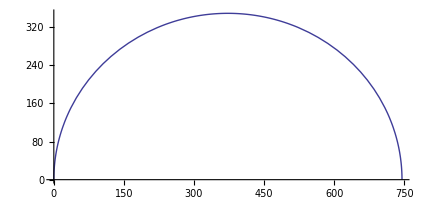

```mathematica
ParametricPlot[{√(260 (2 mp+260)) Cos[α/2]^2,(√(mp 260) Sin[α])/(√2)},{α,0,π}]
```

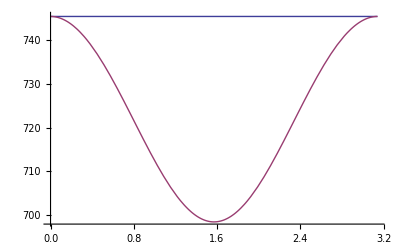

```mathematica
Plot[{√(2mp 260+260^2),Norm[RelP[260,α]]},{α,0,π}]
```

```mathematica
T1[T_,α_]:=T Cos[α/2]^2
T2[T_,α_]:=T Sin[α/2]^2
θ1[m_,T_,α_]:=ArcTan[√(T (2 m+T)) Cos[α/2]^2,(√(m T) Sin[α])/(√2)]
θ2[m_,T_,α_]:=ArcTan[√(T (2 m+T)) Sin[α/2]^2,-(√(m T) Sin[α])/(√2)]
```

```mathematica
ToF[T_,θ_,m_,d_,θd_]:=(d 10^9)/(Cos[θd-θ] √(1-(m/(m+T))^2)c)
```

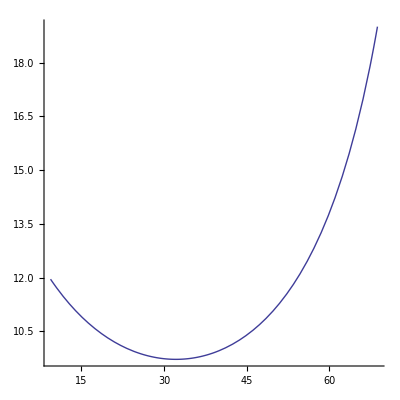

```mathematica
ParametricPlot[{θ1[mp,260,α °] 180/π,ToF[T1[260,α °],θ1[mp,260,α °],mp,1.4,π/3]},{α,20,140},PlotRange->{{20,70},{0,All}},AspectRatio->1]
```

```mathematica
Manipulate[
Plot[{T1[T,α],T2[T,α],T1[T,α]+T2[T,α]},{α,0,π}]
,{m,mp},{T,260}]
```

```mathematica
Manipulate[
Plot[{θ1[m,T,α °] 180/π,(θ1[m,T,α °]-θ2[m,T,α °])180/π},{α,40,140},PlotRange->{84,90},GridLines-> Automatic, Frame->True,FrameLabel->{Style["θ_NN[deg]",20],Style["Δθ_Lab [deg]",20]},PlotLabel->Style["Proton-Proton Elastic Scattering at E_Lab="<>ToString[T]<>" MeV",20],ImageSize->500]
,{m,mp},{{T,260},200,360}]
```

```mathematica
Manipulate[
ParametricPlot[{θ1[m,T,α] 180/π,θ2[m,T,α] 180/π},{α,0,π},AspectRatio->1]
,{m,mp},{{T,260},260,1000}]
```

```mathematica
(*Construction for same mass*)
(* normalized by (total momentum)/2 *)
Manipulate[
Show[
ParametricPlot[{{Cos[θ],Sin[θ]},{  2(Cos[θ/2]^2-1/2),(√(2m))/(√(2 m+T)) Sin[θ]}},{θ,0,2 π},ImageSize->600],
Graphics[{
{Blue,Arrow[{{-1,0},{Cos[α °],Sin[α °]}}]},
{Red,Arrow[{{-1,0},{-Cos[α °],-Sin[α °]}}]},
{Green,Arrow[{{-Cos[α °],-Sin[α °]},{Cos[α °],Sin[α °]}}]},
{Purple,Arrow[{{- 1,0},{ 2(Cos[(α °)/2]^2-1/2),(√(2m))/(√(2 m+T))Sin[α °]}}]},
{Cyan,Arrow[{{- 1,0},{ 2 (Sin[(α °)/2]^2-1/2),-(√(2m))/(√(2 m+T)) Sin[α °]}}]},
{Gray,Arrow[{{ 2 (Sin[(α °)/2]^2-1/2),-(√(2m))/(√(2 m+T)) Sin[α °]},{ 2 (Cos[(α °)/2]^2-1/2),(√(2m))/(√(2 m+T)) Sin[α °]}}]},
{Blue,Text[α/2//N,{Cos[α °],Sin[α °]} {0.9,0.8}]},
{Red,Text[(180-α)/2//N,{-Cos[α °],-Sin[α °]} {0.9,0.8}]},
{Purple,Text[{Norm[{- 1,0}-{ 2(Cos[(α °)/2]^2-1/2),(√(2m))/(√(2 m+T))Sin[α °]}]
,Abs[ArcTan[2 Cos[(α °)/2]^2,√((2m)/(2m+T))Sin[α °]] 180/π]},{ 2 Cos[(α °)/2]^2-1,√((2m)/(2m+T))Sin[α °]} {0.9,0.6}]},{Cyan,Text[{Norm[{- 1,0}-{ 2 (Sin[(α °)/2]^2-1/2),-(√(2m))/(√(2 m+T)) Sin[α °]}]
,Abs[ArcTan[2 Sin[(α °)/2]^2,√((2m)/(2m+T))Sin[α °]] 180/π]},{2 Sin[(α °)/2]^2-1,-√((2m)/(2m+T))Sin[α °]} {0.9,0.6}]},
Text[{α,ArcTan[√(2 m T+T^2)Cos[α °],√(2m T)Sin[α °]] 180/π,√((2m)/(2m+T))},{0.2,0.1}]}
]
],
{{α,90},0,360},{{T,260},0,6000},{{m,mp},{mT,md,mp}}]
```

## The relationship (T, θ) and (T1, θ1)

```mathematica
Solve[{G1==T/(1+x^2),y==√((2m)/(2m+T))x},{T,x}]
```

{{T→(2 (G1 m+G1 m y^2))/(2 m-G1 y^2),x→-(√(-G1 y^2-2 m y^2))/(√(-2 m+G1 y^2))},{T→(2 (G1 m+G1 m y^2))/(2 m-G1 y^2),x→(√(-G1 y^2-2 m y^2))/(√(-2 m+G1 y^2))}}

```mathematica
TiT1[m_,T1_,θ1_]:=(2m)/(((2m)/T1+1)Cos[θ1]^2-1)
θiT1[m_,T1_,θ1_]:=2ArcTan[√((((2m)/T1+1)Sin[θ1]^2)/(((2m)/T1+1)Cos[θ1]^2-1))]
```

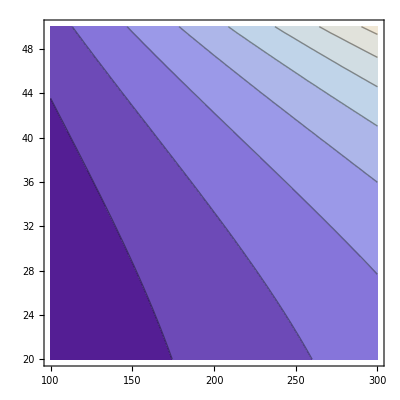

```mathematica
ContourPlot[TiT1[mp,t1,ϕ1 °],{t1,100,300},{ϕ1,20,50}]
```

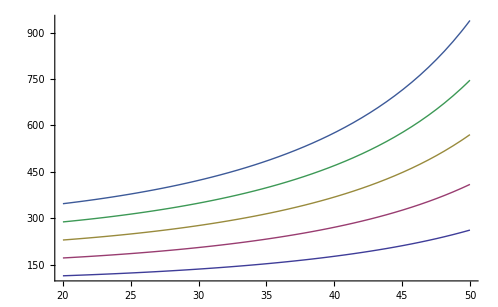

```mathematica
Plot[Evaluate[Table[TiT1[mp,t1,ϕ1 °],{t1,100,300,50}]],{ϕ1,20,50},PlotRange->{0,All}]
```

## The relationship (T, θ) and (T2, θ2)

```mathematica
Solve[{G2==T/(1+x^2),y==-√((2m)/(2m+T))x},{T,x}]
```

{{T→(2 (G2 m+G2 m y^2))/(2 m-G2 y^2),x→-(√(-G2 y^2-2 m y^2))/(√(-2 m+G2 y^2))},{T→(2 (G2 m+G2 m y^2))/(2 m-G2 y^2),x→(√(-G2 y^2-2 m y^2))/(√(-2 m+G2 y^2))}}

```mathematica
TiT2[m_,T2_,θ2_]:=(2m)/(((2m)/T2+1)Cos[θ2]^2-1)
θiT2[m_,T2_,θ2_]:=2ArcTan[√((((2m)/T2+1)Cos[θ2]^2-1)/(((2m)/T2+1)Sin[θ2]^2))]
```

## The relationship (T1, θ1) and (T2, θ2)

```mathematica
T1T2[m_,T2_,θ2_]:=T2(((2m)/T2+1)Sin[θ2]^2)/(((2m)/T2+1)Cos[θ2]^2-1)
θ1θ2[m_,T2_,θ2_]:=ArcTan[Cot[θ2]-(2T2)/(2 m+T2)Csc[2θ2] ]
T2T1[m_,T1_,θ1_]:=T1 (((2m)/T1+1)Sin[θ1]^2)/(((2m)/T1+1)Cos[θ1]^2-1)
θ2θ1[m_,T1_,θ1_]:=ArcTan[Cot[θ1]-(2T1)/(2 m+T1)Csc[2θ1] ]
```

```mathematica
(* Cross Check *)
```

```mathematica
TiT1[mp,T1[300,30°],θ1[mp,300,30 °]]
θiT1[mp,T1[300,30°],θ1[mp,300,30 °]] 180/π
```

300.

30.

```mathematica
Manipulate[
Plot[{θ2θ1[mp,T1,θ1 °] 180/π},{θ1,17,70}, AspectRatio->1]
,{m,mp},{{T1,260},100,1000}]
```

```mathematica
Manipulate[
ParametricPlot[{θ2θ1[mp,T1[T,α °],θ1[mp,T,α °]] 180/π,θ1[mp,T,α °] 180/π},{α,17,70}, AspectRatio->1]
,{m,mp},{{T,260},100,1000}]
```